## Time-dependent bifurcation in a dynamical system

Marko Kocic, 2020-08-16

This notebook accompanies the paper which analyses the mathematical model used when treating the topic of Arctic sea-ice in climate science. The main purpose of the code is to analyse different ODE models and generate the figures for the paper.

Abstract of the paper: Global warming and the increase of greenhouse gases have nearly pushed the Arctic sea-ice system past the critical point, identified by ice-albedo positive feedback. Our work takes the model and applies knowledge from bifurcation theory to identify the behaviour of the ice-albedo positive feedback. In particular, one parameter used in bifurcation theory is attributed to a time component, turning the model into a non-autonomous ordinary differential equation. The results, if applicable to the real world scenario, show a system where, if the Arctic sea-ice system is pushed past its critical point, then the speed at which global warming occurs will not matter. Furthermore, the Arctic sea-ice in any case will melt in a small time window if global warming is not controlled immediately.

## Definitions

Global definitions for this notebook.

```mathematica
$interactive=False;         (* This will evaluate cells with Manipulate[] *)
```

```mathematica
$exportImages=False;       (* To export PDFs *)
```

```mathematica
$plotStreams3D=True;       (* To plot 3D stream lines *)
```

```mathematica
$exportImages3D=False;  (* To export 3D plots *)
```

```mathematica
$fontSize=14;
$imageSize=350;
```

```mathematica
$defaultPlotSettings=Sequence[
PlotTheme->"Scientific",PlotRangePadding->0,ImageSize->$imageSize,
FrameTicksStyle->Directive[$fontSize-1.5,FontFamily->"CMU Serif",Black],
FrameStyle->Directive[$fontSize,FontFamily->"CMU Serif",Black]
];
```

```mathematica
myListLinePlot[data_,params___]:=ListLinePlot[
data,params,
PlotTheme->"Scientific",
FrameTicksStyle->Directive[12,FontFamily->"CMU Serif",Black],PlotRangeClipping->True,
PlotTheme->"Scientific"
]
```

```mathematica
myPlot[data_,params___]:=Plot[
data,params,
PlotTheme->"Scientific",
FrameTicksStyle->Directive[12,FontFamily->"CMU Serif",Black],PlotRangeClipping->True
]
```

## Section 2. Bifurcation theory

The code below handles the plotting of figures for section 2.

### Mathematical background / Perturbation series expansion

```mathematica
printNice[expr_]:=(expr/.{x0->Subscript[x, 0],x1->Subscript[x, 1],x2->Subscript[x, 2],x3->Subscript[x, 3],x4->Subscript[x, 4]})
```

#### Perturbation of x[t] for small ϵ→0 (where x_n[t] are arbitrary functions)

```mathematica
x[t_]:=x0[t]+x1[t] ϵ+1/2 x2[t] ϵ^2+1/6 x3[t] ϵ^3+O[ϵ]^4
```

```mathematica
HoldForm@x[t]==(x[t]//printNice)
```

x[t]==x_0[t]+x_1[t] ϵ+1/2 x_2[t] ϵ^2+1/6 x_3[t] ϵ^3+O[ϵ]^4

#### Expansion of F[x[t]] for small ϵ→0

```mathematica
HoldForm@F[x[t]]==(Series[F[x[t]],{ϵ,0,4}]//printNice)
```

F[x[t]]==F[x_0[t]]+x_1[t] F'[x_0[t]] ϵ+1/2 (x_2[t] F'[x_0[t]]+x_1[t]^2 F''[x_0[t]]) ϵ^2+1/6 (x_3[t] F'[x_0[t]]+3 x_1[t] x_2[t] F''[x_0[t]]+x_1[t]^3 F^(3)[x_0[t]]) ϵ^3+O[ϵ]^4

#### Expansion of x'[t]==F[x[t]] for small ϵ→0

Below are the coefficients collected at the order O[ϵ]^n :

```mathematica
D[Normal@Series[x[t],{ϵ,0,4}],t]-Normal@Series[F[x[t]],{ϵ,0,4}];
coeff={
HoldForm@x'[t]==F[HoldForm@x[t]],
x0'[t]==Simplify[-SeriesCoefficient[%,{ϵ,0,0}]+x0'[t]],
x1'[t]==Simplify[-SeriesCoefficient[%,{ϵ,0,1}]+x1'[t]],
x2'[t]==Simplify[-2SeriesCoefficient[%,{ϵ,0,2}]+ x2'[t]],
x3'[t]==Simplify[-6SeriesCoefficient[%,{ϵ,0,3}]+ x3'[t]]
};
Echo/@%//printNice;
```

x'[t]==F[x[t]]

x0'[t]==F[x0[t]]

x1'[t]==x1[t] F'[x0[t]]

x2'[t]==x2[t] F'[x0[t]]+x1[t]^2 F''[x0[t]]

x3'[t]==x3[t] F'[x0[t]]+3 x1[t] x2[t] F''[x0[t]]+x1[t]^3 F^(3)[x0[t]]

### Saddle-node bifurcation: F(x;a)=a-x^2

```mathematica
useFunction1[expr_]:=Block[{F},F[x_]:=a-x^2;expr]
```

```mathematica
useFunction1b[expr_]:=Block[{F},F[x_]:=-(a-x^2);expr]
```

#### Solution

```mathematica
DSolveValue[D[X[t],t]==F[X[t]]//useFunction1,X[t],t]
```

√a Tanh[√a t+√a C[1]]

#### Perturbations

```mathematica
coeff1=coeff//useFunction1;
Echo/@%//printNice;
```

x'[t]==a-x[t]^2

x0'[t]==a-x0[t]^2

x1'[t]==-2 x0[t] x1[t]

x2'[t]==-2 x1[t]^2-2 x0[t] x2[t]

x3'[t]==-6 x1[t] x2[t]-2 x0[t] x3[t]

```mathematica
sx[t_]=DSolveValue[coeff1⟦2⟧,x0[t],t]//Simplify
```

√a Tanh[√a (t+C[1])]

```mathematica
sx[t]/.a->-a//Simplify[#,Assumptions->a>0]&
```

-√a Tan[√a (t+C[1])]

```mathematica
sx0=xe; (* == ±√a *)
```

```mathematica
sx1=DSolveValue[coeff1⟦3⟧/.{x0[t]->xe},x1[t],t]/.C[1]->C1//Simplify
```

C1 ⅇ^(-2 t xe)

```mathematica
sx2=DSolveValue[coeff1⟦4⟧/.{x0[t]->xe,x1[t]->sx1 },x2[t],t]/.C[1]->C2//Simplify
```

(ⅇ^(-4 t xe) (C1^2+C2 ⅇ^(2 t xe) xe))/xe

```mathematica
sx3=DSolveValue[coeff1⟦5⟧/.{x0[t]->xe,x1[t]->sx1 ,x2[t]->sx2},x3[t],t]/.C[1]->C3//Simplify
```

C3 ⅇ^(-2 t xe)+(3 C1 ⅇ^(-6 t xe) (C1^2+2 C2 ⅇ^(2 t xe) xe))/(2 xe^2)

#### Plots

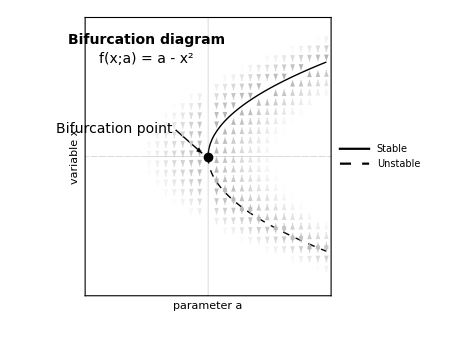

```mathematica
Show[
VectorPlot[
{0,F[x]}//useFunction1,
{a,-2,2},{x,-2,2},
PlotRange->{{-2,2},{-2,2}},
VectorColorFunctionScaling->False,
VectorColorFunction->Function[{x,y,vx,vy,n},GrayLevel[0.7+1.6Norm[{vx,vy}]]],
VectorPoints->29,
VectorScale->{0.03,1,Automatic},
ColorFunctionScaling->False,
ColorFunction->Function[{x,y,vx,vy,n},Blend[{RGBColor[0.9-0.2y,0.85,0.8],White},Norm[{vx,vy}]]],
FrameTicks->None,FrameLabel->{Row@{"parameter ",HoldForm@a},Row@{"variable ",x}},
Epilog->{
Text[Style["Bifurcation diagram",$fontSize,FontFamily->"CMU Serif",Black,Bold],Scaled@{0.25,.92}],
Text[Style[Row@{f,"(",x,";",HoldForm@a,")"," = ",HoldForm@a," - ",x^2},$fontSize,FontFamily->"CMU Serif",Black],Scaled@{0.25,.85}],
Text[Style["Bifurcation point",$fontSize,FontFamily->"CMU Serif",Black],{-0.6,0.42},{1,0}],
Arrow[{{-0.55,0.4},{-0.1,0.05}}],
{PointSize[0.02],Point[{{0,0}}]}
},
Evaluate@$defaultPlotSettings
]/.Arrowheads[{{x_,y_}}]:>Arrowheads[{{0.03,0.5}}]/.Arrow[x___]:>If[Abs@x⟦1,1⟧<0.1,Nothing,Arrow[x]],
Plot[{Sqrt[a],-Sqrt[a]},{a,0,2},
PlotStyle->{{Black,Thick},{Black,Dashed,Thick}},
PlotLegends->Placed[Style[#,$fontSize,FontFamily->"CMU Serif",Black]&/@{"Stable","Unstable"},
Scaled@{0.25,0.2}]
]
]
If[$exportImages,Export[NotebookDirectory[]<>"figure-mk1.pdf",%]]
```

### Transcritical bifurcation: F(x;a)=a x-x^2

```mathematica
useFunction2[expr_]:=Block[{F},F[x_]:=a x-x^2;expr]
```

#### Solution

```mathematica
DSolveValue[D[X[t],t]==F[X[t]]//useFunction2,X[t],t]
```

(a ⅇ^(a t+a C[1]))/(-1+ⅇ^(a t+a C[1]))

```mathematica
s2x[t_,a_,C_]=(a ⅇ^(a t))/(ⅇ^(a t+a C[1])+C[1])/.C[1]->C
```

(a ⅇ^(a t))/(C+ⅇ^(a C+a t))

#### Perturbations

```mathematica
coeff2=coeff//useFunction2;
Echo/@%//printNice;
```

x'[t]==a x[t]-x[t]^2

x0'[t]==a x0[t]-x0[t]^2

x1'[t]==(a-2 x0[t]) x1[t]

x2'[t]==-2 x1[t]^2+(a-2 x0[t]) x2[t]

x3'[t]==-6 x1[t] x2[t]+(a-2 x0[t]) x3[t]

```mathematica
s2x0=xe; (* xe == 0 or xe == a *)
```

```mathematica
s2x1=DSolveValue[coeff2⟦3⟧/.{x0[t]->xe},x1[t],t]/.C[1]->C1//Simplify
```

C1 ⅇ^(t (a-2 xe))

#### Plots

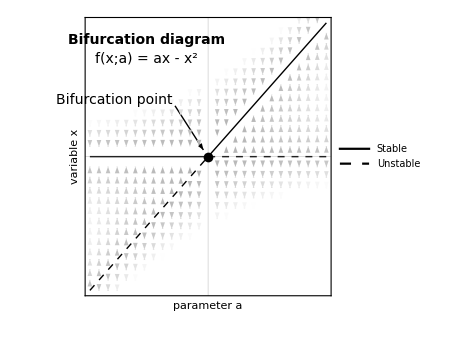

```mathematica
Show[
VectorPlot[
{0,F[x]}//useFunction2,
{a,-2,2},{x,-2,2},
PlotRange->{{-2,2},{-2,2}},
VectorColorFunctionScaling->False,
VectorColorFunction->Function[{x,y,vx,vy,n},GrayLevel[0.7+2Norm[{vx,vy}]]],
VectorPoints->27,
VectorScale->{0.03,1,Automatic},
ColorFunctionScaling->False,
ColorFunction->Function[{x,y,vx,vy,n},Blend[{RGBColor[0.9-0.1(-x+2y),0.85,0.8],White},Norm[{vx,vy}]]],
FrameTicks->None,FrameLabel->{Row@{"parameter ",HoldForm@a},Row@{"variable ",x}},
Epilog->{
Text[Style["Bifurcation diagram",$fontSize,FontFamily->"CMU Serif",Black,Bold],Scaled@{0.25,.92}],
Text[Style[Row@{f,"(",x,";",HoldForm@a,")"," = ",HoldForm@a,x," - ",x^2},$fontSize,FontFamily->"CMU Serif",Black],Scaled@{0.25,.85}],
Text[Style["Bifurcation point",$fontSize,FontFamily->"CMU Serif",Black],{-0.6,0.84},{1,0}],
Arrow[{{-0.56,0.76},{-0.08,0.1}}],
{PointSize[0.02],Point[{{0,0}}]}
},
Evaluate@$defaultPlotSettings
]/.Arrowheads[{{x_,y_}}]:>Arrowheads[{{0.03,0.5}}]/.Arrow[x___]:>If[Abs@x⟦1,1⟧<0.1,Nothing,Arrow[x]],
Plot[{
Piecewise[{{a,a>0}},0],
Piecewise[{{a,a<0}},0]
},{a,-2,2},
PlotStyle->{{Black,Thick},{Black,Dashed,Thick}},
PlotLegends->Placed[Style[#,$fontSize,FontFamily->"CMU Serif",Black]&/@{"Stable","Unstable"},Scaled@{0.75,0.2}]
]
]
If[$exportImages,Export[NotebookDirectory[]<>"figure-mk2.pdf",%]]
```

### Time-dependent transcritical bifurcation: F(x,a)=a(t) x-x^2 where a(t)=a_0+A t

```mathematica
useFunction3[expr_]:=Block[{F},F[x_]:=(a0+A t) x-x^2;expr]
```

#### Solution

```mathematica
s3x[a_,A_,a0_,C_]=DSolveValue[D[X[t],t]==F[X[t]]//useFunction3,X[t],t]/.t->(a-a0)/A/.C[1]->C//Simplify
s3x$t[t_,A_,a0_,C_]=s3x[a0+A t,A,a0,C]//Simplify
```

(2 √A ⅇ^(a^2/(2 A)))/(2 √A C ⅇ^(a0^2/(2 A))+√(2 π) Erfi[a/(√2 √A)])

(2 √A ⅇ^((a0+A t)^2/(2 A)))/(2 √A C ⅇ^(a0^2/(2 A))+√(2 π) Erfi[(a0+A t)/(√2 √A)])

#### Perturbations

```mathematica
coeff3=coeff//useFunction3;
Echo/@%//printNice;
```

x'[t]==(a0+A t) x[t]-x[t]^2

x0'[t]==(a0+A t) x0[t]-x0[t]^2

x1'[t]==(a0+A t-2 x0[t]) x1[t]

x2'[t]==-2 x1[t]^2+(a0+A t-2 x0[t]) x2[t]

x3'[t]==-6 x1[t] x2[t]+(a0+A t-2 x0[t]) x3[t]

```mathematica
s3x0=xe; (* ==√a *)
```

(0.282843 ⅇ^(25. (-1+0.02 t)^2))/(2.03661×10^11+√(2 π) Erfi[5. (-1+0.02 t)])

C1 ⅇ^(1. a0 t+0.5 A t^2+(1.62498×10^11+Erfi[5.-0.1 t] (-2.-2. Log[8.12488×10^10-1. Erfi[5.-0.1 t]])+1.62498×10^11 Log[8.12488×10^10-1. Erfi[5.-0.1 t]])/(-8.12488×10^10+Erfi[5.-0.1 t]))

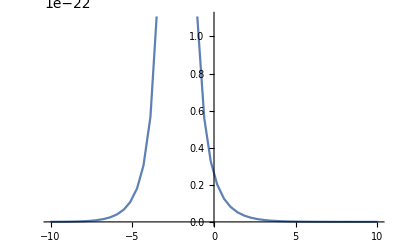

```mathematica
s3x$t[t,0.02,-1,10]
s3x1=DSolveValue[coeff3⟦3⟧/.{x0[t]->%},x1[t],t]/.C[1]->C1//Simplify
Plot[s3x1/.a0->-1/.A->0.01/.C1->1,{t,-10,10}]
```

#### Helper functions

```mathematica
findIntegrationConstant[A_,a0_,x0_,params___]:=
Quiet@Block[{C},
C/.FindRoot[s3x[Rationalize@a0,Rationalize@A,Rationalize@a0,C]==Rationalize@x0,{C,5},params]
]
```

```mathematica
findVerticalAsymptote[A_,a0_,C_]:=
Quiet@Block[{a},
a/.FindRoot[Denominator[s3x[a,A,a0,C]]==0,{a,C}]
]
```

#### Plots

```mathematica
Block[{
range=2.5,ϵ=0.03,
C1=0,C2=-2,C3=+2,
a0=-1,A=0.1,
a1,a2,a3
},
a1=findVerticalAsymptote[A,a0,C1];
a2=findVerticalAsymptote[A,a0,C2];
a3=findVerticalAsymptote[A,a0,C3];
Show[
VectorPlot[
{A,F[x]}//useFunction2,
{a,-range,range},{x,-range,range},
PlotRange->range{{-1,1},{-1,1}},
VectorColorFunctionScaling->False,
VectorColorFunction->Function[{x,y,vx,vy,n},GrayLevel[0.79+0.5Norm[{vx,vy}]]],
VectorPoints->27,
VectorScale->{0.03,1,Automatic},
FrameTicks->None,FrameLabel->{Row@{"variable ",HoldForm@a},Row@{"variable ",x}},
Epilog->{
{White,Opacity[0.95],EdgeForm[Directive[GrayLevel[0.9]]],Rectangle[Scaled@{0.02,0.96},Scaled@{0.43,0.77},RoundingRadius->0.05]},
Text[Style["Vector field plot",$fontSize,FontFamily->"CMU Serif",Black,Bold],Scaled@{0.23,.92}],
Text[Style[Row@{f,"(",x,",",HoldForm@a,")"," = ",HoldForm@a,x," - ",x^2},$fontSize,FontFamily->"CMU Serif",Black],Scaled@{0.23,.86}],
Text[Style[Row@{HoldForm@a,"(",t,") = ",a0," + ",A," ",t},$fontSize,FontFamily->"CMU Serif",Black],Scaled@{0.23,.8}]
},
Evaluate@$defaultPlotSettings
]/.Arrowheads[{{x_,y_}}]:>Arrowheads[{{0.03,0.5}}],
Plot[{
Piecewise[{{s3x[a,A,a0,C1],a>a1+ϵ}},Indeterminate],
Piecewise[{{s3x[a,A,a0,C2],a>a2+ϵ}},Indeterminate],
Piecewise[{{s3x[a,A,a0,C3],a>a3+ϵ}},Indeterminate],
Piecewise[{{s3x[a,A,a0,C1],a<a1-ϵ}},Indeterminate],
Piecewise[{{s3x[a,A,a0,C2],a<a2-ϵ}},Indeterminate],
Piecewise[{{s3x[a,A,a0,C3],a<a3-ϵ}},Indeterminate],
Piecewise[{{a,a>0}},Indeterminate],
Piecewise[{{a,a<0}},0],
Piecewise[{{0,a<0}},Indeterminate]
},{a,-range,range},PlotRange->{{-range,range},{-range,range}},
Exclusions->{a1,a2,a3},
PlotStyle->{
{Magenta},{Blue},{Red},
{Magenta,Dashed},{Blue,Dashed},{Red,Dashed},
{Black,Thick},{Black,Dashed,Thick},{Black,Dashed,Thick}}
]
]
]
If[$exportImages,Export[NotebookDirectory[]<>"figure-mk3a.pdf",%]]
```

-Graphics-

#### Stream plot

```mathematica
Block[{
range=2.5,ϵ=0.03,pts,
C1=0,C2=-2,C3=+2,
a0=-1,A=0.1,
a1,a2,a3,
showSol =Indeterminate
},
a1=findVerticalAsymptote[A,a0,C1];
a2=findVerticalAsymptote[A,a0,C2];
a3=findVerticalAsymptote[A,a0,C3];
pts=Join[
Table[{a,range-0.5},{a,-range,range,0.25}],
Table[{a,-range+0.5},{a,-range,range,0.25}],
Table[{a,0.4},{a,range-1,range,0.25}],
Table[{-a,-0.4},{a,range-1,range,0.25}]
];
Show[
StreamPlot[
{A,F[x]}//useFunction2,
{a,-range,range},{x,-range,range},
PlotRange->0.8{{-range,range},{-range,range}},
StreamPoints->{pts,1,30},
MaxRecursion->1,PerformanceGoal->"Quality",StreamScale->0.07,
StreamColorFunction->"Rainbow",
PlotTheme->"Scientific",PlotRangePadding->0,ImageSize->$imageSize,
Epilog->{
{White,Opacity[0.9],EdgeForm[Directive[GrayLevel[0.9]]],Rectangle[Scaled@{0.05,0.96},Scaled@{0.4,0.76},RoundingRadius->0.05]},
Text[Style["Stream plot",$fontSize,FontFamily->"CMU Serif",Black,Bold],Scaled@{0.23,.92}],
Text[Style[Row@{f,"(",x,",",HoldForm@a,")"," = ",HoldForm@a,x," - ",x^2},$fontSize,FontFamily->"CMU Serif",Black],Scaled@{0.23,.86}],
Text[Style[Row@{HoldForm@a,"(",t,") = ",a0," + ",A," ",t},$fontSize,FontFamily->"CMU Serif",Black],Scaled@{0.23,.8}]
},
FrameTicks->None,FrameLabel->{Row@{"variable ",HoldForm@a},Row@{"variable ",x}},
Evaluate@$defaultPlotSettings
],
Plot[{
Piecewise[{{showSol s3x[a,A,a0,C1],a>a1+ϵ}},Indeterminate],
Piecewise[{{showSol s3x[a,A,a0,C2],a>a2+ϵ}},Indeterminate],
Piecewise[{{showSol s3x[a,A,a0,C3],a>a3+ϵ}},Indeterminate],
Piecewise[{{showSol s3x[a,A,a0,C1],a<a1-ϵ}},Indeterminate],
Piecewise[{{showSol s3x[a,A,a0,C2],a<a2-ϵ}},Indeterminate],
Piecewise[{{showSol s3x[a,A,a0,C3],a<a3-ϵ}},Indeterminate],
Piecewise[{{a,a>0}},Indeterminate],
Piecewise[{{a,a<0}},0],
Piecewise[{{0,a<0}},Indeterminate]
},{a,-range,range},PlotRange->{{-range,range},{-range,range}},
Exclusions->{0,a1,a2},
PlotStyle->{
{Magenta},{Blue},{Red},
{Magenta,Dashed},{Blue,Dashed},{Red,Dashed},
{Black,Thick},{Black,Dashed,Thick},{Black,Dashed,Thick}}
]
]]
If[$exportImages,Export[NotebookDirectory[]<>"figure-mk3b.pdf",%]]
```

-Graphics-

#### Bifurcation diagram

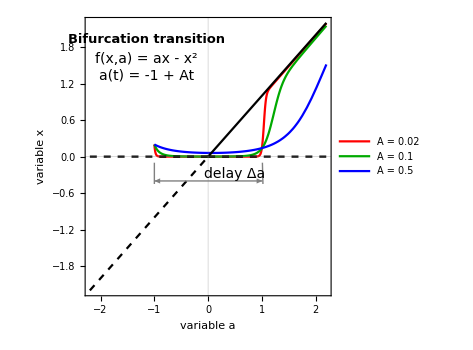

```mathematica
Block[{
A,C ,
a0=-1,x0=0.2,
A1=0.02,A2=0.1,A3=0.5,
c1,c2,c3,
range=2.2,rangeΔ=0.3,
wp=20
},
c1=findIntegrationConstant[A1,a0,x0,WorkingPrecision->wp];
c2=findIntegrationConstant[A2,a0,x0,WorkingPrecision->wp];
c3=findIntegrationConstant[A3,a0,x0,WorkingPrecision->wp];
Plot[{
Piecewise[{{s3x[a,A1,a0,c1],a>a0}},Indeterminate],
Piecewise[{{s3x[a,A2,a0,c2],a>a0}},Indeterminate],
Piecewise[{{s3x[a,A3,a0,c3],a>a0}},Indeterminate],
Piecewise[{{a,a>0}},Indeterminate],
Piecewise[{{a,a<0}},0],
Piecewise[{{0,a<0}},Indeterminate]
},{a,-range,range},PlotRange->{{-range,range},{-range,range}},
PlotTheme->"Scientific",PlotRangePadding->0,ImageSize->$imageSize,
PlotStyle->{
{Red},{Darker@Green},{Blue},
{Black},{Black,Dashed},{Black,Dashed}},
PlotLegends->Placed[Style[#,$fontSize,FontFamily->"CMU Serif",Black,Background->White]&/@{
Row@{HoldForm@A," = ",A1},
Row@{HoldForm@A," = ",A2},
Row@{HoldForm@A," = ",A3}
},Scaled@{0.75,0.18}],
PlotRange->0.8{{-range,range},{-range,range}},AspectRatio->1,
Epilog->{
Text[Style["Bifurcation transition",$fontSize-1,FontFamily->"CMU Serif",Black,Bold],Scaled@{0.25,.92}],
Text[Style[Row@{f,"(",x,",",HoldForm@a,")"," = ",HoldForm@a,x," - ",x^2},$fontSize,FontFamily->"CMU Serif",Black],Scaled@{0.25,.85}],
Text[Style[Row@{HoldForm@a,"(",t,") = ",a0," + ",HoldForm@A,t},$fontSize,FontFamily->"CMU Serif",Black],Scaled@{0.25,.79}],
{Gray,Arrowheads[{-.03,.03}],Arrow[{{-1,-0.4},{1.01,-0.4}}],
Line[{{-1,-0.45},{-1,-0.1}}],Line[{{1.02,-0.45},{1.01,-0.1}}],
Text[Style[Row@{"delay Δ",a},14,Black,FontFamily->"CMU Serif"],{0.5,-0.29}]
}
},
FrameTicks->None,FrameLabel->{Row@{"variable ",HoldForm@a},Row@{"variable ",x}},
Evaluate@$defaultPlotSettings
]]
If[$exportImages,Export[NotebookDirectory[]<>"figure-mk3c.pdf",%]]
```

#### Time evolution of x(t)

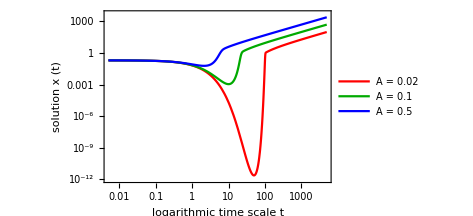

```mathematica
Block[{
A,C ,
a0=-1,x0=0.2,
A1=0.02,A2=0.1,A3=0.5,
c1,c2,c3,
range=5000,rangeΔ=0.3,
wp=20
},
c1=findIntegrationConstant[A1,a0,x0,WorkingPrecision->wp];
c2=findIntegrationConstant[A2,a0,x0,WorkingPrecision->wp];
c3=findIntegrationConstant[A3,a0,x0,WorkingPrecision->wp];
LogLogPlot[{
s3x$t[t,A1,a0,c1],
s3x$t[t,A2,a0,c2],
s3x$t[t,A3,a0,c3]
},{t,0.005,range},
PlotRange->{{0.005,range},{10^-12,5000}},
PlotTheme->"Scientific",PlotRangePadding->0,ImageSize->$imageSize,
PlotStyle->{
{Red},{Darker@Green},{Blue}
},
PlotLegends->Placed[Style[#,$fontSize,FontFamily->"CMU Serif",Black,Background->White]&/@{
Row@{HoldForm@A," = ",A1},
Row@{HoldForm@A," = ",A2},
Row@{HoldForm@A," = ",A3}
},Scaled@{0.25,0.25}],
Epilog->{
},
FrameLabel->{Row@{"logarithmic time scale ",HoldForm@t},Row@{"solution  ",x," (",t,")"}},
Evaluate@$defaultPlotSettings
]]
If[$exportImages,Export[NotebookDirectory[]<>"figure-mk3d.pdf",%]]
```

#### Rate of change Δx/Δa

```mathematica
s3x$tPrim[t_,A_,a0_,c1_]:=Derivative[1,0,0,0][s3x$t][t,Rationalize@A,Rationalize@a0,c1]/Rationalize@A;
```

Peaks: (Δt,ΔA) = {{101.895,2.03791},{22.2242,2.22242},{6.30325,3.15162}}

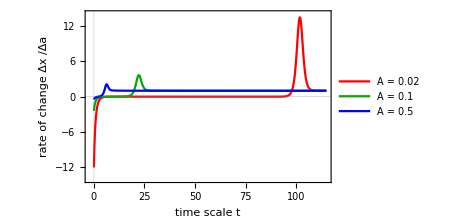

```mathematica
Block[{
A,C ,
a0=-1,x0=0.2,
A1=0.02,A2=0.1,A3=0.5,
c1,c2,c3,
t1,t2,t3,
range=115,rangeΔ=0.3,
wp=20
},
c1=findIntegrationConstant[A1,a0,x0,WorkingPrecision->wp];
c2=findIntegrationConstant[A2,a0,x0,WorkingPrecision->wp];
c3=findIntegrationConstant[A3,a0,x0,WorkingPrecision->wp];
t1=ArgMax[s3x$tPrim[t,A1,a0,c1],t];
t2=ArgMax[s3x$tPrim[t,A2,a0,c2],t];
t3=ArgMax[s3x$tPrim[t,A3,a0,c3],t];
Echo@Row@{"Peaks: (Δt,ΔA) = " ,Thread[{{t1,t2,t3}-0//N, {a0+A1* t1,a0+A2 *t2,a0+A3* t3}-a0//N}]};
Plot[Evaluate@{
s3x$tPrim[t,A1,a0,c1],
s3x$tPrim[t,A2,a0,c2],
s3x$tPrim[t,A3,a0,c3]
},{t,0,range},
PlotRange->{{-2,range},{-14,14}},
PlotTheme->"Scientific",PlotRangePadding->0,ImageSize->$imageSize,
PlotStyle->{
{Red},{Darker@Green},{Blue}
},
PlotLegends->Placed[Style[#,$fontSize,FontFamily->"CMU Serif",Black,Background->White]&/@{
Row@{HoldForm@A," = ",N@A1},
Row@{HoldForm@A," = ",N@A2},
Row@{HoldForm@A," = ",N@A3}
},Scaled@{0.25,0.25}],
Epilog->{
},
WorkingPrecision->wp,
FrameLabel->{Row@{"time scale ",HoldForm@t},Row@{"rate of change  ",Δ,x," /",Δ,a}},
Evaluate@$defaultPlotSettings
]]
If[$exportImages,Export[NotebookDirectory[]<>"figure-mk3e.pdf",%]]
```

#### Interactive stream plot explorer

```mathematica
If[$interactive,Manipulate[Block[{range=2.5,rangeΔ=0.3,
a0=-1,A=CA
},
Show[
StreamPlot[
{A,F[x]}//useFunction2,
{a,-range,range},{x,-range,range},
PlotRange->0.8{{-range,range},{-range,range}},
StreamPoints->ControlActive[Coarse,Fine],
MaxRecursion->1,PerformanceGoal->"Quality",StreamScale->0.07,
StreamColorFunction->"Rainbow",
PlotTheme->"Scientific",PlotRangePadding->0,ImageSize->$imageSize,
Epilog->{
{White,Opacity[0.8],Rectangle[Scaled@{0.05,0.96},Scaled@{0.4,0.75}]},
Text[Style["Stream plot",$fontSize,FontFamily->"CMU Serif",Black,Bold],Scaled@{0.23,.92}],
Text[Style[Row@{f,"(",x,",",HoldForm@a,")"," = ",HoldForm@a,x," - ",x^2},$fontSize,FontFamily->"CMU Serif",Black],Scaled@{0.23,.86}],
Text[Style[Row@{HoldForm@a,"(",t,") = ",a0," + ",A," ",t},$fontSize,FontFamily->"CMU Serif",Black],Scaled@{0.23,.8}]
},
FrameTicks->None,FrameLabel->{Row@{"variable ",HoldForm@a},Row@{"variable ",x}},
Evaluate@$defaultPlotSettings
]
]],
{{CA,0.1,"A"},-0.5,0.5,0.05,Exclusions->{0}}
]]
```

## Section 4. Results of the practical work

This section is a newer variant of the plotting not relying on CSV-files. Since we already know what the bifurcation diagram is supposed to look like from the results of the Python code we may take some liberties in plotting the figure.

### The time-dependent Budyko model

```mathematica
plotModLinBudyko[cϵ_:0,type_:VectorPlot]:=Block[
{
(* Functions *)
	f,g,α,vf$T,vf$ΔF,T,ΔF,
(* Physical parameters *)
	λ=0.612,
	σ=5.670374419×10^-8,
	S=1360.8,
	Cp=1,
(* Albedo parameters *)
	ice=0.55,
	water =0.3,
	meltpoint=273.15,
	variance = 10,
(* ΔF parameters *)
	ϵ=cϵ,
(* Fixed and bifurcation points *)
	fixedPoints,bifP1,bifP2,ix1,ix2,ϕ
},
(* Albedo function *)
f[x_]:=Exp[-1/x]/;x>0;
f[x_]:=0/;x≤0;
g[x_]:=f[x]/(f[x]+f[1-x]);
α[T_]:=(water-ice)*g[(T-(meltpoint-variance))/(2*variance)]+ice;

(* Vector field *)
vf$T[ΔF_,T_]:=(1/Cp)((1/4)S(1-α[T])-λ σ T^4+ΔF);
vf$ΔF[ΔF_,T_]:=ϵ;

(* Steady-state *)
ReplaceAll[Plot[
Cp vf$T[0,T],{T,230,320}
],Line[{list___}]:>Line[{fixedPoints={list}}]];
fixedPoints=fixedPoints/.{x_,y_}:>{-y,x};

(* Min/Max from the list *)
bifP1=TakeSmallestBy[Select[fixedPoints,260<#⟦2⟧<290&],#⟦1⟧&,1]⟦1⟧;
bifP2=TakeLargestBy[Select[fixedPoints,260<#⟦2⟧<290&],#⟦1⟧&,1]⟦1⟧;
{ix1,ix2}=Sort[{
Position[fixedPoints,bifP1,1]⟦1,1⟧,
Position[fixedPoints,bifP2,1]⟦1,1⟧
}];

(* Min/Max from the function *)
bifP1=Quiet@ArgMin[{vf$T[0,T],260<T<280},T];
bifP2=Quiet@ArgMax[{vf$T[0,T],260<T<280},T];
bifP1={-((1/4)S(1-α[T])-λ σ T^4),T}/.T->bifP1;
bifP2={-((1/4)S(1-α[T])-λ σ T^4),T}/.T->bifP2;

Quiet@type[
{
vf$ΔF[ΔF,T],vf$T[ΔF,T]
},
{ΔF,-30,30},
{T,235,305},
PlotRange->{{-30+0.5,30-0.5},{235+0.5,305-0.5}},
MaxRecursion->1,PerformanceGoal->"Quality",StreamScale->0.07,
Sequence@@If[type===VectorPlot,{
VectorColorFunctionScaling->False,
VectorColorFunction->Function[{x,y,vx,vy,n},GrayLevel[0.6+0.5Norm[{vx,vy}]]],
VectorPoints->27,
VectorScale->{0.03,1,Automatic}
},{
StreamPoints->ControlActive[Coarse,{1000,0.5,50}]
}]//Evaluate,
Axes->{False,False},AspectRatio->0.9,
PlotTheme->"Scientific",PlotRangePadding->0,ImageSize->$imageSize,
FrameLabel->{
Style[Row@{Δ,F,"/","(W/",("m")^2,")"},$fontSize,FontFamily->"CMU Serif",Black],
Style[Row@{T,"/K"},$fontSize,FontFamily->"CMU Serif",Black]},
Epilog->{
{White,Opacity[0.95],EdgeForm[Directive[GrayLevel[0.9]]],Rectangle[Scaled@{0.02,0.98},Scaled@{0.63,0.85},RoundingRadius->0.5]},
Text[Style["Bifurcation diagram of",$fontSize,FontFamily->"CMU Serif"],Scaled@{0.33,.94}],
Text[Style[Row@{"the time-independent model"},$fontSize,FontFamily->"CMU Serif"],Scaled@{0.33,.88}],
{Blue,Thick,Line[fixedPoints⟦;;ix1⟧],Line[fixedPoints⟦ix2;;⟧],
Line[{Scaled@{0.55,0.2},Scaled@{0.7,0.2}}],Black,
Text[Style["Stable",$fontSize-1,FontFamily->"CMU Serif"],Scaled@{0.73,0.2},{-1,0}]
},
{Blue,Thick,Dashed,Line[fixedPoints⟦ix1;;ix2⟧],
Line[{Scaled@{0.55,0.13},Scaled@{0.7,0.13}}],Black,
Text[Style["Unstable",$fontSize-1,FontFamily->"CMU Serif"],Scaled@{0.73,0.13},{-1,0}]
},
{PointSize[0.02],Point[bifP1],Point[bifP2]}
},
Evaluate@$defaultPlotSettings
]
] 
plotModLinBudyko[0]
If[$exportImages,Export[NotebookDirectory[]<>"figure-bifurcation.pdf",%]]
```

-Graphics-

```mathematica
If[$interactive,Manipulate[
plotModLinBudyko[cϵ,StreamPlot],
{{cϵ,0,"ϵ"},0,1,0.01}
]]
```

### 3D streamplots of the time-dependent Budyko model

We use StreamPlot4D from: https://raw.githubusercontent.com/mekeetsa/StreamPlot4d/master/StreamPlot4D.m

```mathematica
Get[NotebookDirectory[]<>"StreamPlot4D.m"]
```

```mathematica
plotModLinBudyko3D[cϵ_:0,vf$t_:1,funcType_:0,pts_:4]:=Block[
{
(* Functions *)
	f,g,α,vf$T,vf$ΔF,T,ΔF,t,
	scale$ΔF,scale$T,invScale$ΔF,invScale$T,
(* Physical parameters *)
	λ=Rationalize@0.612,
	σ=Rationalize@5.670374419×10^-8,
	S=Rationalize@1360.8,
	Cp=Rationalize@1,
(* Albedo parameters *)
	ice=Rationalize@0.55,
	water =Rationalize@0.3,
	meltpoint=Rationalize@273.15,
	variance =Rationalize@ 10,
(* ΔF parameters *)
	ϵ=cϵ,
(* Fixed and bifurcation points *)
	fixedPoints,fixedPoints2,bifP1,bifP2,ix1,ix2,ϕ
},
(* Albedo function *)
f[x_]:=Exp[-1/x]/;x>0;
f[x_]:=0/;x≤0;
g[x_]:=f[x]/(f[x]+f[1-x]);
α[T_]:=(water-ice)*g[(T-(meltpoint-variance))/(2*variance)]+ice;

(* Vector field *)
vf$T[ΔF_,T_,t_]:=(1/Cp)((1/4)S(1-α[T])-λ σ T^4+ΔF);
Switch[funcType,
1,vf$ΔF[ΔF_,T_,t_]:=ϵ 2t, (* quadratic *)
2,vf$ΔF[ΔF_,T_,t_]:=ϵ/( 2 √(1+t)), (* sublinear *)
3,vf$ΔF[ΔF_,T_,t_]:=ϵ /(1+t), (* logarithmic *)
0,vf$ΔF[ΔF_,T_,t_]:=ϵ  (* linear; constant if ϵ == 0 *)
];

scale$ΔF[ΔF_]:=10ΔF;
scale$T[T_]:=235+(T+3)/6*(305-235);
invScale$ΔF[ΔF_]:=ΔF/10;
invScale$T[T_]:=-3+(T-235)/(305-235)*6;

(* Steady-state *)
ReplaceAll[Plot[
Cp vf$T[0,T,t],{T,230,320}
],Line[{list___}]:>Line[{fixedPoints={list}}]];

(* Min/Max from the list *)
bifP1=TakeSmallestBy[Select[fixedPoints,260<#⟦1⟧<290&],#⟦2⟧&,1]⟦1⟧;
bifP2=TakeLargestBy[Select[fixedPoints,260<#⟦1⟧<290&],#⟦2⟧&,1]⟦1⟧;
{ix1,ix2}=Sort[{
Position[fixedPoints,bifP1,1]⟦1,1⟧,
Position[fixedPoints,bifP2,1]⟦1,1⟧
}];

fixedPoints2=fixedPoints/.{x_,y_}:>{invScale$ΔF[-y]/3,-1,invScale$T[x]/3};
fixedPoints=fixedPoints/.{x_,y_}:>{invScale$ΔF[-y]/3,1,invScale$T[x]/3};

Quiet@Show[
StreamPlot4D[
{
0,
vf$ΔF[scale$ΔF@ΔF,scale$T@T,t]/10^4,
vf$t,
vf$T[scale$ΔF@ΔF,scale$T@T,t]/10^4
},
{τ,-3,-2.999},
{ΔF,-3,3},
{t,0,240},
{T,-3,3},
VectorPoints->0,
StreamColorFunction->(Blend[{{-30,Red},{240,Blue}},#⟦3⟧]&),
ProjectionTo3D->({#⟦2⟧,#⟦3⟧,#⟦4⟧}(0.99-0*0.5(#⟦1⟧+3)/6)&),
StreamPoints->Tuples[{{0},Range[-3,3,3/pts],{0},Range[-3,3,3/pts]}],
StreamArrowheads->Range[0,1,0.1],
PlotRange->Automatic,PlotRangePadding->{Scaled[0.01],Scaled[0.001],Scaled[0.01]},
Boxed->False,Boxed4D->True,ImageSize->350,
BaseStyle->{FontFamily->"Cambria",FontSize->14},
Axes4DLabels->{"",Row@{Δ,F},HoldForm@t,HoldForm@T},
ViewPoint->{0,  -2.4,0},ViewAngle->30°,
Box4DStyle->{GrayLevel[0.2],Opacity[0.2]}
],
Graphics3D[{
{Blue,Thick,Line[fixedPoints⟦;;ix1⟧],Line[fixedPoints⟦ix2;;⟧]},
{Blue,Dashed,Line[fixedPoints⟦ix1;;ix2⟧]},
{Opacity[0.1],Red,Line[fixedPoints2⟦;;ix1⟧],Line[fixedPoints2⟦ix2;;⟧]},
{Opacity[0.1],Red,Dashed,Line[fixedPoints2⟦ix1;;ix2⟧]}
}]
]
]
```

```mathematica
If[$plotStreams3D,plot3d1=plotModLinBudyko3D[0,0.15,0];
If[$exportImages3D,
Export[NotebookDirectory[]<>"figure-3D-1.png",plot3d1,ImageResolution->300],
Rasterize[plot3d1,ImageResolution->150]
]]
```

-Graphics-

```mathematica
If[$plotStreams3D,
plot3d2=plotModLinBudyko3D[1,0.08,0];
If[$exportImages3D,
Export[NotebookDirectory[]<>"figure-3D-2.png",plot3d2,ImageResolution->300],
Rasterize[plot3d2,ImageResolution->150]
]]
```

-Graphics-

```mathematica
If[$plotStreams3D,
plot3d3=plotModLinBudyko3D[0.025,0.08,1];
If[$exportImages3D,
Export[NotebookDirectory[]<>"figure-3D-3.png",plot3d3,ImageResolution->300],
Rasterize[plot3d3,ImageResolution->150]
]]
```

-Graphics-

```mathematica
If[$plotStreams3D,
plot3d4=plotModLinBudyko3D[1,0.08,3];
If[$exportImages3D,
Export[NotebookDirectory[]<>"figure-3D-4.png",plot3d4,ImageResolution->300],
Rasterize[plot3d4,ImageResolution->150]
]]
```

-Graphics-

## Old Code section

The code below is older code from previous revisions when plotting was handled using CSV-files. This code is also not updated so choice of variable names and execution of the code is not the cleanest.

### Plot figures — Parameter definitions

Old global parameters from a previous Mathematica Notebook.

```mathematica
Quiet@Clear[S,α,σ,λ,tp,tpy,t,a,b,x,d1];
```

```mathematica
(* Constants and functions for the model *)
S=1360.8;
α=0.55;
σ=5.670374419*10^(-8);
λ=0.612;
(*tp=0;*)
tp = 20;
tpy = 265.80814374417383; 
d1[t_,a_,b_] := a*t+b;
```

### Plot figures — Albedo as a function of time

```mathematica
Quiet@Clear[f,g,h,ice,water,meltpoint,variance,T];
```

Older Albedo function whose function name is ‘h’ instead of ‘α’.

```mathematica
ice=0.55;
water =0.3;
meltpoint=273.15;
variance = 10;
f[t_]:=If[t≤0,0,E^(-1/t)];
g[t_]:=f[t]/(f[t]+f[1-t]);
h[t_]:=(water-ice)*g[(t-(meltpoint-variance))/(2*variance)]+ice;
```

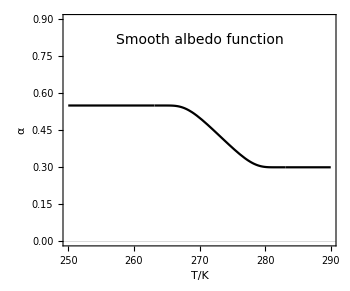

```mathematica
myPlot[
{h[T]},{T,250,290},
PlotRange->{{250,290},{0,0.9}},
PlotStyle->{Black},
FrameLabel->{
Style[Row@{T,"/K"},14,FontFamily->"CMU Serif",Black],
Style[Row@{HoldForm@α},14,FontFamily->"CMU Serif",Black]},
Epilog->{
Text[Style["Smooth albedo function",14,FontFamily->"CMU Serif",Black],Scaled@{0.5,.89}],
},
ImageSize->350,
AspectRatio->1/1.2
]
If[$exportImages,Export[NotebookDirectory[]<>"figure-albedo.pdf",%]]
```

### Create figures — dT/dt as a function of T

This figure is never used in the paper.

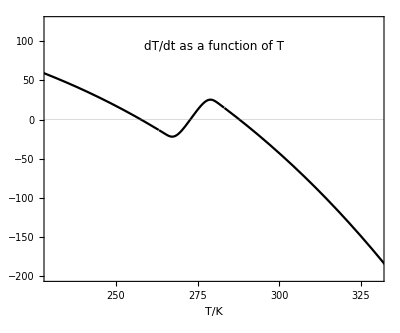

```mathematica
plotModel = myPlot[
{S/4(1-h[T])-λ*σ*T^4},{T,200,370},
PlotRange->{{230,330},{-200,125}},
PlotStyle->{Black},
FrameLabel->{
Style[Row@{T,"/K"},15,FontFamily->"CMU Serif",Black],
Style[Row@{},14,FontFamily->"CMU Serif",Black]},
Epilog->{
Text[Style[Row@{"dT/dt", " as a function of ",T},12,FontFamily->"CMU Serif",Black],Scaled@{0.5,.89}],

},
ImageSize->400,
AspectRatio->1/1.2
]
```

### Create figures — Numerical solution to dT/dt

```mathematica
ass1=NDSolve[{T'[t]==S/4(1-h[T[t]])-λ*σ*T[t]^4 ,T[0]==270},T,{t,0,100}];
ass2=NDSolve[{T'[t]==S/4(1-h[T[t]])-λ*σ*T[t]^4 ,T[0]==275},T,{t,0,100}];
```

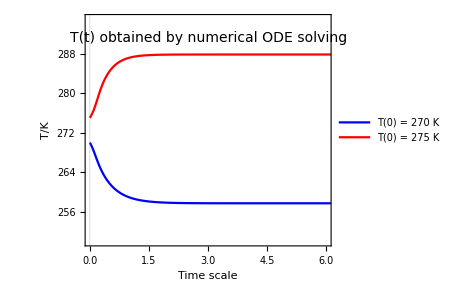

```mathematica
myPlot[
{Evaluate[T[t]/.ass1],Evaluate[T[t]/.ass2]},{t,0,100},
PlotRange->{{0,6},{250,295}},
PlotStyle->{Blue,Red},
PlotLegends->Placed[Style[#,13,FontFamily->"CMU Serif",Black]&/@{Row@{T,"(0) = 270 K"},Row@{T,"(0) = 275 K"}},{0.75,0.5}],
FrameLabel->{
Style[Row@{"Time scale"},14,FontFamily->"CMU Serif",Black],
Style[Row@{T,"/K"},14,FontFamily->"CMU Serif",Black]},
Epilog->{
Text[Style[Row@{T,"(",t,")"," obtained by numerical ODE solving"},14,FontFamily->"CMU Serif",Black],Scaled@{0.5,.9}],

},
ImageSize->350,
AspectRatio->1/1.2
]
If[$exportImages,Export[NotebookDirectory[]<>"figure-ODE.pdf",%]]
```

### Create figures — Linear ΔF

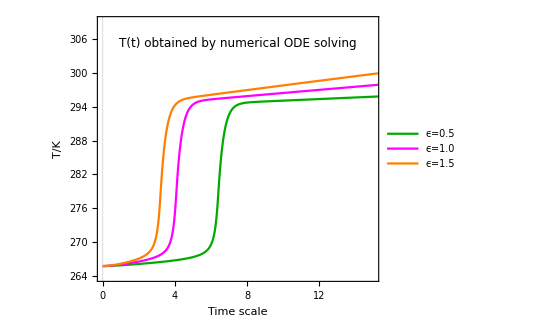

```mathematica
Quiet@Clear[T,t,s,u,v,w,x];
s=NDSolve[{T'[t]==S/4(1-h[T[t]])-λ*σ*T[t]^4 +tp+0.5*t,T[0]==tpy},T,{t,0,100}];
u=NDSolve[{T'[t]==S/4(1-h[T[t]])-λ*σ*T[t]^4 +tp+t,T[0]==tpy},T,{t,0,100}];
v=NDSolve[{T'[t]==S/4(1-h[T[t]])-λ*σ*T[t]^4 +tp+1.5*t,T[0]==tpy},T,{t,0,100}];

plotExampleODE=myPlot[
{Evaluate[T[t]/.s],Evaluate[T[t]/.u],Evaluate[T[t]/.v]},{t,0,100},
PlotRange->{{0,15},{264,309}},
PlotStyle->{Darker@Green,Magenta,Orange},
PlotLegends->Placed[{"ϵ=0.5","ϵ=1.0","ϵ=1.5"},{0.85,0.3}],
FrameLabel->{
Style[Row@{"Time scale"},15,FontFamily->"CMU Serif",Black],
Style[Row@{T,"/K"},14,FontFamily->"CMU Serif",Black]},
Epilog->{
Text[Style[Row@{T,"(",t,")"," obtained by numerical ODE solving"},12,FontFamily->"CMU Serif",Black],Scaled@{0.5,.9}]
},
ImageSize->400,
AspectRatio->1/1.2
]
```

### Plot figures — Get the results from CSV and plot the bifurcation diagram

Old plotting code that reads the results from a CSV-file.

```mathematica
getCSV[timeIndependentCSV_,csvFileList___]:=
Block[
{dataPts,breaks},
dataPts=Import[NotebookDirectory[]<>"data/"<>timeIndependentCSV<>".csv"];
breaks=Join[{1},Table[If[Length@dataPts⟦n⟧<2,n,Nothing],{n,Length@dataPts}]];
Join[
Table[
dataPts⟦breaks⟦n⟧+1;;breaks⟦n+1⟧-1⟧,
{n,Length@breaks-1}
],
Import[NotebookDirectory[]<>"data/"<>#<>".csv"]&/@{csvFileList}
]
]
```

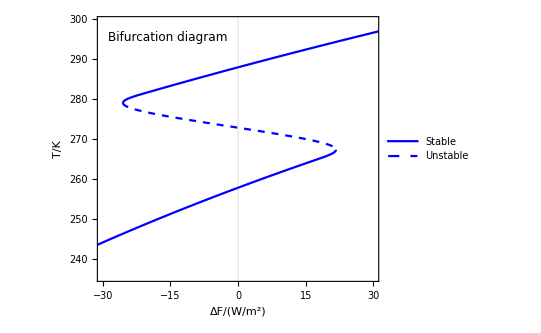

```mathematica
myListLinePlot[
Evaluate@getCSV["notime"]⟦1;;3⟧,
PlotRange->{{-30,30},Automatic},
PlotStyle->{Blue,{Blue,Dashed},{Blue}},
PlotLegends->Placed[LineLegend[{Blue, {Blue,Dashed}},{"Stable","Unstable"}],{0.8,0.2}],
FrameLabel->{
Style[Row@{Δ,F,"/","(W/",("m")^2,")"},15,FontFamily->"CMU Serif",Black],
Style[Row@{T,"/K"},14,FontFamily->"CMU Serif",Black]},
Epilog->{
Text[Style["Bifurcation diagram",12,FontFamily->"CMU Serif",Black],Scaled@{0.25,.92}],
},
AspectRatio->1/1.2,
ImageSize->400
]
```

### Create figures — Multiple CSV-files

Example used is Tipping Point Prevention. All of the figures in Section 4 b

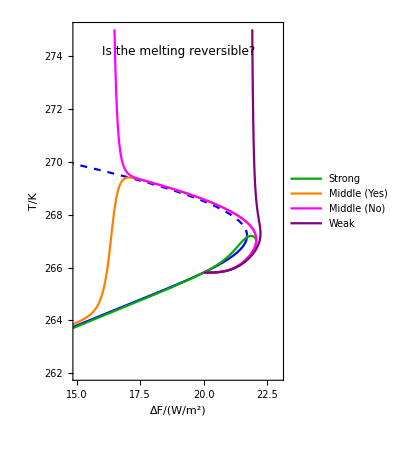

```mathematica
myListLinePlot[
Evaluate@getCSV["notime","catchyes","catchbarelyno","catchbarelyyes","catchno"],
PlotRange->{{15,23},{262,275}},
PlotStyle->{Blue,{Blue,Dashed},Blue,Darker@Green,Orange,Magenta,Purple},
PlotLegends->Placed[LineLegend[{Darker@Green,Orange,Magenta,Purple},{"Strong","Middle (Yes)","Middle (No)","Weak"}],{0.8,0.15}],
FrameLabel->{
Style[Row@{Δ,F,"/(","W/",("m")^2,")"(*," ili sta se nalazi na x osi ⟶"*)},15,FontFamily->"CMU Serif",Black],
Style[Row@{T,"/K"(*" ili sta se nalzi na y osi ⟶"*)},14,FontFamily->"CMU Serif",Black]},
Epilog->{
Text[Style["Is the melting reversible?",12,FontFamily->"CMU Serif",Black],Scaled@{0.5,.92}]
},
AspectRatio->1.5,
ImageSize->300
]
If[$exportImages,Export[NotebookDirectory[]<>"figure-reversibleClose.pdf",%]]
```

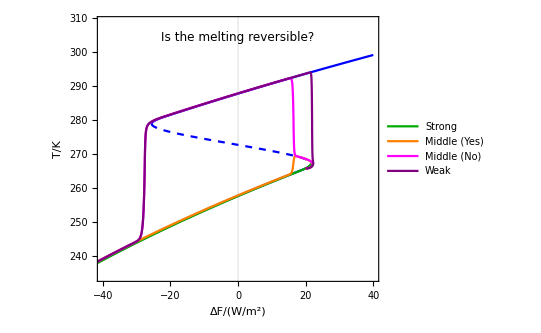

```mathematica
myListLinePlot[
Evaluate@getCSV["notime","catchyes","catchbarelyno","catchbarelyyes","catchno"],
PlotRange->{{-40,40},{234,309}},
PlotStyle->{Blue,{Blue,Dashed},Blue,Darker@Green,Orange,Magenta,Purple},
PlotLegends->Placed[LineLegend[{Darker@Green,Orange,Magenta,Purple},{"Strong","Middle (Yes)","Middle (No)","Weak"}],{0.85,0.18}],
FrameLabel->{
Style[Row@{Δ,F,"/(","W/",("m")^2,")"(*," ili sta se nalazi na x osi ⟶"*)},15,FontFamily->"CMU Serif",Black],
Style[Row@{T,"/K"(*" ili sta se nalzi na y osi ⟶"*)},14,FontFamily->"CMU Serif",Black]},
Epilog->{
Text[Style["Is the melting reversible?",12,FontFamily->"CMU Serif",Black],Scaled@{0.5,.92}]
},
ImageSize->400,
AspectRatio->1/1.2
]
If[$exportImages,Export[NotebookDirectory[]<>"figure-reversible.pdf",%]]
```